```mathematica
probdens[x_,t_,d_]:=1/(2 d^2)π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2)
```

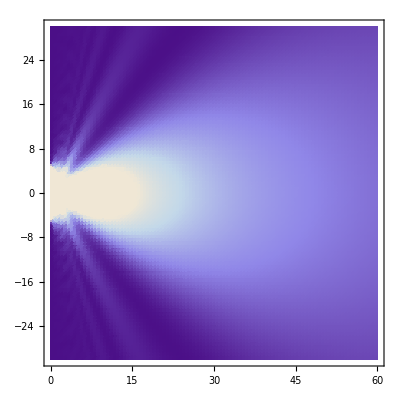

```mathematica
DensityPlot[probdens[y,x,7],{x,0,60},{y,-30,30},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

```mathematica
VelocityField3[x_, t_, d_ ]:=-(√(2/π) Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))
```

```mathematica
ddd = 7.0;
www=1.0;
kkk = 1.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-VelocityField3[y[t], t, ddd ]2,y[0.1]== RandomVariate[UniformDistribution[{-ddd,ddd}]]},y,{t,1,100}],{200}];
Plot[{(y[t]/2)/.HollandtablU},{t,1,100}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```